#### Singlet-Fermion Majorana Dark Matter (SFDM)

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

XX⟶ e-e+

```mathematica
T2DM2F=CreateTopologies[0,2->2,ExcludeTopologies->{SelfEnergies,Tadpoles}];
(*Paint[T2DM2F];*)
```

Only the thirt fermion family...

loading generic model file /home/anferivera/Work/FeynArts-3.9/Models/SFDM_FA.gen

> $GenericMixing is OFF

generic model {SFDM_FA} initialized

loading classes model file /home/anferivera/Work/FeynArts-3.9/Models/SFDM_FA.mod

> 46 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 169 vertices

classes model {SFDM_FA} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 2 Particles insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

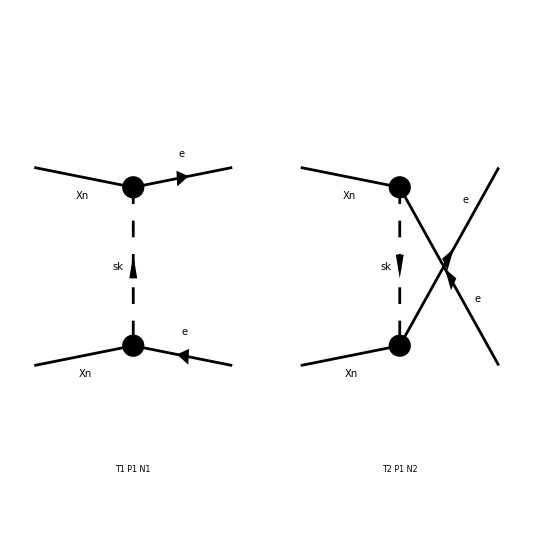

FeynArtsGraphics[{Xn,Xn}→{e,e}][([T1 P1 N1] | [T2 P1 N2] | Null
Null | Null | Null
Null | Null | Null)]

```mathematica
n22=InsertFields[T2DM2F,{F[13],F[13]}->{F[4],-F[4]},InsertionLevel->{Particles},Model->"SFDM_FA", GenericModel->"SFDM_FA",ExcludeParticles->{}];
Paint[n22]
```

#### Amplitude

```mathematica
resultn22=CalcFeynAmp[CreateFeynAmp[n22],FermionChains->VA,Antisymmetrize->False,Invariants->True];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-7.frm

running FORM...

ok

```mathematica
Den[x_,y_]:= 1/(x-y) 
expr1=Simplify[ComplexExpand[ Plus@@resultn22//.Subexpr[]//.Abbr[]//.M$FACouplings]]
```

1/(8 (Msk^2-T) (Msk^2-U))gL^2 ((T-U) Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]+(2 Msk^2-T-U) Mat[(<v1|5,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]+T Mat[(<v1|1,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)]-U Mat[(<v1|1,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)]+2 Msk^2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)]-T Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)]-U Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)])

#### Check divergencias

```mathematica
uvcheck=UVDivergentPart[expr1]//Simplify
FreeQ[uvcheck,Divergence]
```

0

True

#### Momentas in the computation

Conservación of the energy-momentum for the massles final fermion state

```mathematica
cons=Solve[E1==m*Sqrt[1+v^2]&&E1==E2,{E2,E1}][[1]]

k1={E1,m*v,0,0}/.cons
k2={E1,-m*v,0,0}/.cons
k3={E2,Sqrt[E2^2-mf^2]*st,Sqrt[E2^2-mf^2]*ct,0}//.cons
k4={E2,-Sqrt[E2^2-mf^2]*st,-Sqrt[E2^2-mf^2]*ct,0}//.cons
```

{E2→m √(1+v^2),E1→m √(1+v^2)}

{m √(1+v^2),m v,0,0}

{m √(1+v^2),-m v,0,0}

{m √(1+v^2),st √(-mf^2+m^2 (1+v^2)),ct √(-mf^2+m^2 (1+v^2)),0}

{m √(1+v^2),-st √(-mf^2+m^2 (1+v^2)),-ct √(-mf^2+m^2 (1+v^2)),0}

#### Mandelstan variables

```mathematica
guv={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};

MV={S->(k1+k2).guv.(k1+k2),
T->(k1-k3).guv.(k1-k3),
U->(k1-k4).guv.(k1-k4)};
MV//MatrixForm
```

(S→4 m^2 (1+v^2)
T→-ct^2 (-mf^2+m^2 (1+v^2))+(m v-st √(-mf^2+m^2 (1+v^2))) (-m v+st √(-mf^2+m^2 (1+v^2)))
U→-ct^2 (-mf^2+m^2 (1+v^2))+(-m v-st √(-mf^2+m^2 (1+v^2))) (m v+st √(-mf^2+m^2 (1+v^2))))

#### Dirac matrices

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
gamma5={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
gammamu={gamma0,gamma1,gamma2,gamma3,gamma5};
k11=k1.guv.{gamma0,gamma1,gamma2,gamma3};
k15=gamma5.(k1.guv.{gamma0,gamma1,gamma2,gamma3});
```

```mathematica
gammamu[[3]]
```

{{0,0,0,-ⅈ},{0,0,ⅈ,0},{0,ⅈ,0,0},{-ⅈ,0,0,0}}

Old definition for the  χ

```mathematica
(*χ[s_]:=IdentityMatrix[2][[(1-s)/2+1]]*)
```

#### Spin

```mathematica
χ[s_]:=If[s==1,{1,0},{0,1}]
```

```mathematica
χ[1]
χ[-1]
```

{1,0}

{0,1}

#### Spinores (Cheng appendix)

```mathematica
σpi=((Total[k1[[#+1]]PauliMatrix[#]&/@Range[3]])/(k1[[1]]+m));
σpf=((Total[k3[[#+1]]PauliMatrix[#]&/@Range[3]])/(k3[[1]]+mf));
```

```mathematica
uspinor[s_,eif_,mif_]:=Sqrt[k3[[1]]+mif]ArrayFlatten[{χ[s],Dot[eif,χ[s]]},1]
uspinor[1,σpi,m]
uspinor[1,σpf,mf]
```

{√(m+m √(1+v^2)),0,0,(m v)/(√(m+m √(1+v^2)))}

{√(mf+m √(1+v^2)),0,0,(ⅈ ct √(-mf^2+m^2 (1+v^2))+st √(-mf^2+m^2 (1+v^2)))/(√(mf+m √(1+v^2)))}

```mathematica
vspinor[s_,eif_,mif_]:=Sqrt[k4[[1]]+mif]ArrayFlatten[{-Dot[eif,χ[s]],χ[s]},1]
vspinor[1,σpi,m]
vspinor[1,σpf,mf]
```

{0,-(m v)/(√(m+m √(1+v^2))),√(m+m √(1+v^2)),0}

{0,-(ⅈ ct √(-mf^2+m^2 (1+v^2))+st √(-mf^2+m^2 (1+v^2)))/(√(mf+m √(1+v^2))),√(mf+m √(1+v^2)),0}

Check normaliation for the U and V Spinors

```mathematica
Simplify[Simplify[(Conjugate[uspinor[1,σpi,m]].gamma0).uspinor[1,σpi,m],Element[{mf,m,v,st,ct,MDF,y,√(mf+m √(1+v^2)),1/(√(mf+m √(1+v^2))),√(-mf^2+m^2 (1+v^2)),1/(√m),√m},Reals]]/.(ct^2+st^2)->1]
```

2 m

Check normaliation for the V Spinors

```mathematica
Simplify[Simplify[(Conjugate[vspinor[1,σpi,m]].gamma0).vspinor[1,σpi,m],Element[{mf,m,v,st,ct,MDF,y,√(mf+m √(1+v^2)),1/(√(mf+m √(1+v^2))),√(-mf^2+m^2 (1+v^2)),√m,1/(√m)},Reals]]/.(ct^2+st^2)->1]
```

-2 m

#### Amplitude (mf->0)

```mathematica
expr2=Simplify[expr1/.MV/.mf->0/.st->Sqrt[1-ct^2],m>0]
```

1/(4 (Msk^4+2 m^2 Msk^2 (1+2 v^2)+m^4 (1+4 ct^2 (v^2+v^4))))gL^2 (2 √(1-ct^2) m^2 v √(1+v^2) Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]+(m^2+Msk^2+2 m^2 v^2) Mat[(<v1|5,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]+2 √(1-ct^2) m^2 v √(1+v^2) Mat[(<v1|1,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)]+m^2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)]+Msk^2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)]+2 m^2 v^2 Mat[(<v1|5,Lor[1]|u2>) (<u3|5,Lor[1]|v4>)])

Amplitude that depend of the spin si {i, 1, 2, 3, 4}

```mathematica
AMPS[s1_,s2_,s3_,s4_]:=Simplify[Simplify[
expr2//.{
Mat[DiracChain[Spinor[k[1],MDF,-1],1,Lor[1],Spinor[k[2],MDF,1]]*DiracChain[Spinor[k[3],Me,1],1,Lor[1],Spinor[k[4],Me,-1]]]->Simplify[Total[
Dot[Dot[Conjugate[vspinor[s1,σpi,m]],Dot[gamma0,gammamu[[#]]]].uspinor[s2,σpi,m]]*Dot[Dot[Conjugate[vspinor[s3,σpf,m]],Dot[gamma0,gammamu[[#]]]].uspinor[s4,σpf,m]]
&/@Range[4]],Element[{mf,st,ct,m,v},Reals]],
Mat[DiracChain[Spinor[k[1],MDF,-1],5,Lor[1],Spinor[k[2],MDF,1]]*DiracChain[Spinor[k[3],Me,1],1,Lor[1],Spinor[k[4],Me,-1]]]->Simplify[Total[
Dot[Dot[Conjugate[vspinor[s1,σpi,m]],Dot[Dot[gamma0,gamma5],gammamu[[#]]]].uspinor[s2,σpi,m]]*Dot[Dot[Conjugate[vspinor[s3,σpf,m]],Dot[gamma0,gammamu[[#]]]].uspinor[s4,σpf,m]]
&/@Range[4]],Element[{mf,st,ct,m,v},Reals]],
Mat[DiracChain[Spinor[k[1],MDF,-1],1,Lor[1],Spinor[k[2],MDF,1]]*DiracChain[Spinor[k[3],Me,1],5,Lor[1],Spinor[k[4],Me,-1]]]->Simplify[Total[
Dot[Dot[Conjugate[vspinor[s1,σpi,m]],Dot[gamma0,gammamu[[#]]]].uspinor[s2,σpi,m]]*Dot[Dot[Conjugate[vspinor[s3,σpf,m]],Dot[Dot[gamma0,gamma5],gammamu[[#]]]].uspinor[s4,σpf,m]]
&/@Range[4]],Element[{mf,st,ct,m,v},Reals]],
Mat[DiracChain[Spinor[k[1],MDF,-1],5,Lor[1],Spinor[k[2],MDF,1]]*DiracChain[Spinor[k[3],Me,1],5,Lor[1],Spinor[k[4],Me,-1]]]->Simplify[Total[
Dot[Dot[Conjugate[vspinor[s1,σpi,m]],Dot[Dot[gamma0,gamma5],gammamu[[#]]]].uspinor[s2,σpi,m]]*Dot[Dot[Conjugate[vspinor[s3,σpf,m]],Dot[Dot[gamma0,gamma5],gammamu[[#]]]].uspinor[s4,σpf,m]]
&/@Range[4]],Element[{mf,st,ct,m,v},Reals]]
}/.MV/.st->Sqrt[1-ct^2],Element[{ct,st,mf,m,√(-mf^2+m^2 (1+v^2))},Reals]],m>0]
```

```mathematica
(*AMP=Simplify[Sum[Sum[Sum[Sum[AMPS[i,j,k,l],{i,0,1}],{j,0,1}],{k,0,1}],{l,0,1}],Element[{1/(√(m (1+√(1+v^2)))),√(m (1+√(1+v^2))),√(1+v^2),√(1+√(1+v^2))},Reals]]*)
```

```mathematica
AMP=Simplify[Simplify[AMPS[1,-1,1,-1],Element[{1/(√(m (1+√(1+v^2)))),√(m (1+√(1+v^2))),√(1+v^2),√(1+√(1+v^2))},Reals]]/.mf->0]
```

(gL^2 m v ((-ⅈ ct+√(1-ct^2)) m^2 (1+√(1+v^2)) (√(1+v^2) √(m^2 (1+v^2))+√(m^2 (1+v^2)^2))+(-ⅈ ct+√(1-ct^2)) Msk^2 (1+√(1+v^2)) (√(1+v^2) √(m^2 (1+v^2))+√(m^2 (1+v^2)^2))+2 (-ⅈ ct+√(1-ct^2)) m^2 v^2 (1+√(1+v^2)) (√(1+v^2) √(m^2 (1+v^2))+√(m^2 (1+v^2)^2))+4 √(1-ct^2) m^3 (1+v^2)^(3/2) (ct (ct+ⅈ √(1-ct^2)) (1+√(1+v^2))+(-1+ct^2+ⅈ ct √(1-ct^2)) (1+v^2+√(1+v^2)))))/(2 (1+v^2) (Msk^4+2 m^2 Msk^2 (1+2 v^2)+m^4 (1+4 ct^2 (v^2+v^4))))

#### Phase space factor

```mathematica
F1=Simplify[(1/(64*π^2*S)*√(((S-(2*mf)^2)(S-(mf-mf)^2))/((S-(m+m)^2)(S-(m-m)^2))))/.MV]
Simplify[Series[F1,{v,0,4}],m>0]
```

(√(1+(1-mf^2/m^2)/v^2))/(256 m^2 π^2 (1+v^2))

(√(m^2-mf^2))/(256 m^3 π^2 v)+((-m^2+2 mf^2) v)/(512 m^3 √(m^2-mf^2) π^2)+((3 m^4-12 m^2 mf^2+8 mf^4) v^3)/(2048 m^3 (m^2-mf^2)^(3/2) π^2)+O[v]^5

Forma alterna del espacio de fase

```mathematica
F11=Simplify[Sqrt[  k3[[2]]^2+k3[[3]]^2+k3[[4] ]^2/.st->Sqrt[1-ct^2]]/(64*Pi^2*k1[[1]]^2*Sqrt[S]*2*v)/.MV]
Simplify[Series[F11,{v,0,4}],m>0]
```

(√(-mf^2+m^2 (1+v^2)))/(256 π^2 v (m^2 (1+v^2))^(3/2))

(√(m^2-mf^2))/(256 m^3 π^2 v)+((-2 m^2+3 mf^2) v)/(512 m^3 √(m^2-mf^2) π^2)+((8 m^4-24 m^2 mf^2+15 mf^4) v^3)/(2048 (m^4-m^2 mf^2)^(3/2) π^2)+O[v]^5

#### dσ/dΩ

```mathematica
F2=Simplify[Simplify[(F1*AMP*Conjugate[AMP])/.mf->0,Element[{Msk,gL,mf,m,v,st,ct,MDF,y,√(1-ct^2),√(m (1+v^2))},Reals]],m>0]
```

(gL^4 m^2 √(1+1/v^2) v^2 (2+v^2+2 √(1+v^2)) (Msk^4+2 m^2 Msk^2 (-1+2 ct^2 (1+v^2))+m^4 (1+4 ct^4 (v^2+v^4))))/(256 π^2 (1+v^2) (Msk^4+2 m^2 Msk^2 (1+2 v^2)+m^4 (1+4 ct^2 (v^2+v^4)))^2)

```mathematica
F3=Simplify[Series[F2,{v,0,2}]]
```

(gL^4 m^2 (m^4+2 (-1+2 ct^2) m^2 Msk^2+Msk^4) v)/(64 (m^2+Msk^2)^4 π^2)+O[v]^3

#### σ(v)=∫ (dσ/dΩ)dΩ

```mathematica
Integrate[((F3*2Pi*Sin[t])//.{st->Sin[t],ct->Cos[t]}),{t,0,Pi}]
sigma=Simplify[Normal[Series[%,{v,0,5}]],v>0]
```

(gL^4 m^2 (3 m^4-2 m^2 Msk^2+3 Msk^4) v)/(48 (m^2+Msk^2)^4 π)

(gL^4 m^2 (3 m^4-2 m^2 Msk^2+3 Msk^4) v)/(48 (m^2+Msk^2)^4 π)

#### σ .vr

```mathematica
sigmavr=Collect[((sigma*vr)/.v->(vr/2)),{vr,vr^2}]
```

(gL^4 m^2 (3 m^4-2 m^2 Msk^2+3 Msk^4) vr^2)/(96 (m^2+Msk^2)^4 π)

#### Comparation with : arXiv : 1307.6480 (Scalar Dark Matter Models with Significant Internal Bremsstrahlung)

```mathematica
Collect[Simplify[Series[sigmavr//.{Msk->r*m},{mf,0,2}]],{vr,vr^2}]
```

(gL^4 (3-2 r^2+3 r^4) vr^2)/(96 m^2 π (1+r^2)^4)

WARNING!!! →     Debe dar:  (gL^4 (1+ r^4) vr^2)/(48 m^2 π (1+r^2)^4)